```mathematica
(* data sets: 365, 436, 577 are wavelengths in nm that give values for {voltage, current}  *)
data365= {{-1.1,0},{4.1, 84*10^(-10)},{9.1, 168*10^(-10)},{14.1, 236*10^(-10)},{19.1, 281*10^(-10)},{24.1, 331*10^(-10)}, {30.71, 378*10^(-10)}};
```

```mathematica
data436 = {{-0.76,0},{2.78,23*10^(-10)},{4.74, 36*10^(-10)},{6.78, 43*10^(-10)},{8.77, 50*10^(-10)},{10.78, 58*10^(-10)},{12.76, 65*10^(-10)}};
```

```mathematica
data577 = {{-0.02,0},{5, 212*10^(-11)},{10.02, 284*10^(-11)},{15.03, 350*10^(-11)},{20.04, 398*10^(-11)},{25.02, 436*10^(-11)},{30.72, 436*10^(-11)}};
Needs["ErrorBarPlots`"]
```

```mathematica
(*data365 plot with and line graph*)
```

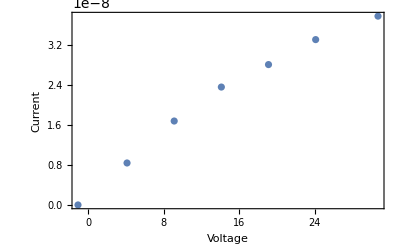

```mathematica
ListPlot[ data365, PlotRange->All,Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

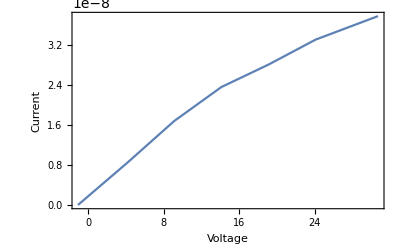

```mathematica
ListPlot[data365, PlotRange->All, Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
(*graph in the form of y=mx+b for data365*)
```

```mathematica
Fit[data365, {1,x}, x]
```

4.07336×10^-9+1.19155×10^-9 x

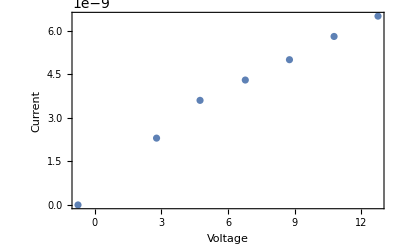

```mathematica
(*data436 plot with and line graph*)

ListPlot[data436, PlotRange->All, Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

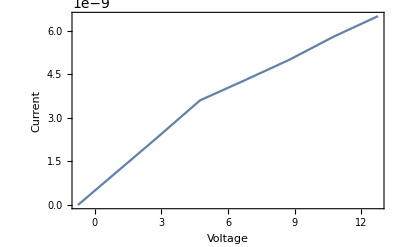

```mathematica
ListPlot[data436, PlotRange->All, Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
(*graph in the form of y=mx+b for data436*)
```

```mathematica
Fit[data436, {1,x}, x]
```

8.7035×10^-10+4.66904×10^-10 x

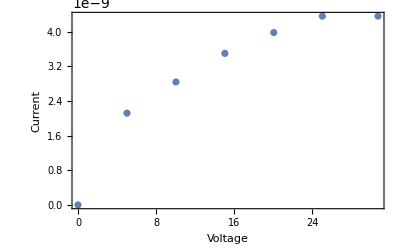

```mathematica
(*data577 plot with and line graph*)

ListPlot[data577, PlotRange->All, Frame -> True,
 FrameLabel ->{"Voltage", "Current"}]
```

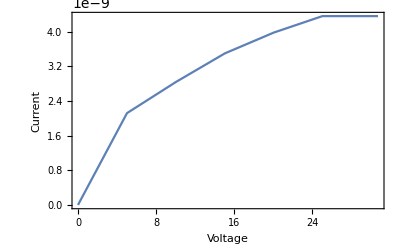

```mathematica
ListPlot[data577, PlotRange->All, Frame -> True,
 FrameLabel ->{"Voltage", "Current"}, Joined -> True]
```

```mathematica
(*graph in the form of y=mx+b for data577*)
```

```mathematica
Fit[data577, {1,x}, x]
```

1.04571×10^-9+1.30801×10^-10 x